```mathematica
(* PARTICLE OSCILLATING ON A ROTATING RING *)

Remove["Global`*"]

SetAttributes[{ω,R,g,m},Constant]

(* Lagrangian found by hand *)
lag=1/2 m(R^2 θ'[t]^2+ω^2 R^2 Sin[θ[t]]^2)-m g R(1-Cos[θ[t]]);

(* Defining Euler-Lagrange *)
EL[q_]:=D[lag,q]-Dt[D[lag,D[q,t]],t]==0

(* Finding equation of motion *)
eqnmotion=EL[θ[t]];
inConds={θ[0]==π/4,θ'[0]==0};

Print[EL[θ[t]]//Simplify]

(* Finding solution to equation of motion numerically *)
m=1;
R=2;
g=10;
ω=5;
(* By setting θ''[t] to zero, we can find equilibrium θ. We find mathematicall that *)
(* if ω^2>g/R, we have 4 eq (top, bottom, others), but only two if < (top, bottom only *)

soln=NDSolve[{eqnmotion,inConds},θ,{t,0,100}][[1]];

x[t_]:=R Sin[θ[t]]Cos[ω t]/.soln
y[t_]:=R Sin[θ[t]]Sin[ω t]/.soln
z[t_]:=-R Cos[θ[t]]/.soln

ParametricPlot3D[{x[t],y[t],z[t]},{t,0,50},PlotRange->{{-1.5R,1.5R},{-1.5R,1.5R},{-1.5R,1.5R}},Background->Black,PlotStyle->Green,AxesStyle->White,AxesLabel->{x,y,z}]
```

m R ((-g+R ω^2 Cos[θ[t]]) Sin[θ[t]]-R θ''[t])==0

-Graphics3D-

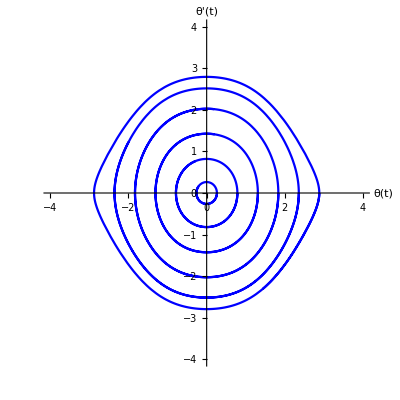

```mathematica
(* PHASE DIAGRAM FOR ω^2 < g/R *)
Remove["Global`*"]

m=1;
R=5;
g=10;
ω=1;

(* Lagrangian *)
lag=1/2 m(R^2 θ'[t]^2+ω^2 R^2 Sin[θ[t]]^2)-m g R(1-Cos[θ[t]]);
(* Euler-Lagrange *)
EL[q_]:=D[lag,q]-Dt[D[lag,D[q,t]],t]==0

eqnmotion=EL[θ[t]];
begang=Table[(n π)/12,{n,1,12,2}];
numang=Length[begang];


soln=Table[NDSolve[{eqnmotion,θ'[0]==0,θ[0]==begang[[i]]},θ,{t,0,100}],{i,1,numang}];

eqnsToPlot=Table[{θ[t]/.soln[[i]],θ'[t]/.soln[[i]]},{i,1,numang}];


ParametricPlot[
{eqnsToPlot},
{t,0,10},
PlotRange->{{-4,4},{-4,4}},
PlotStyle->Blue,
AxesLabel->{θ[t],θ'[t]}]
```

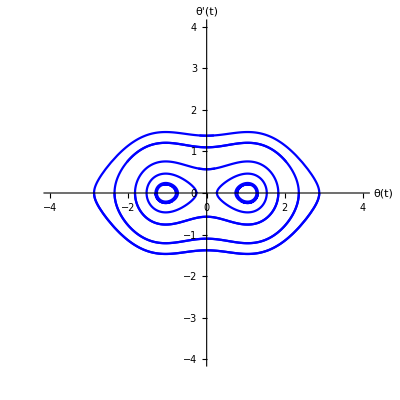

```mathematica
(* PHASE DIAGRAM FOR ω^2 > g/R *)
Remove["Global`*"]

m=1;
R=20;
g=10;
ω=1;

(* Lagrangian *)
lag=1/2 m(R^2 θ'[t]^2+ω^2 R^2 Sin[θ[t]]^2)-m g R(1-Cos[θ[t]]);
(* Euler-Lagrange *)
EL[q_]:=D[lag,q]-Dt[D[lag,D[q,t]],t]==0

eqnmotion=EL[θ[t]];
begang=Table[(n π)/12,{n,1,12,2}];
numang=Length[begang];


soln=Table[NDSolve[{eqnmotion,θ'[0]==0,θ[0]==begang[[i]]},θ,{t,0,100}],{i,1,numang}];

eqnsToPlot=Table[{{θ[t]/.soln[[i]],θ'[t]/.soln[[i]]},{-θ[t]/.soln[[i]],θ'[t]/.soln[[i]]}},{i,1,numang}];


ParametricPlot[
{eqnsToPlot},
{t,0,10},
PlotRange->{{-4,4},{-4,4}},
PlotStyle->Blue,
AxesLabel->{θ[t],θ'[t]}]
```